#### Exercise 2:

Here we are looking at the first parametrization: f(t) = (Cos(t), Sin(t)). We can find the tangent vector of this parametrization by taking the derivative of this function of the unit circle:

f'(t) = (-Sin(t), Cos(t)), 0≤t≤2π

And to calculate the length of the tangent vector:

√(-(Sin(t))^2+ (Cos(t))^2)= 1

Thus the length of the tangent vector for the unit circle is 1

Likewise for the second parametrization:  g(t) = (Cos(t^2), Sin(t^2))

g'(t) = (-Sin(t^2)2t, Cos(t)2t), 0≤t≤√(2π)

And the length:
											√((-Sin(t^2)2t)^2+ (Cos(t^2)2t)^2)= 2t

To explain why the first quadrant of the g[x] graph is more accurate than the first quadrant of the f[x] graph we need to take a look at the speed of which the particle in accordance to g is travelling. Now, the line segments are obtained by dividing the time interval into 12 pieces--meaning each segment represents the movement of the particle during one of those subintervals. Now, since the particle in g(t) picks up speed at a slower rate at first compared to the f(t) graph, it will have much smaller, but more precise line segments that more accurately depict the circle. However, the g(t) derivative portrays the speed at which the particle moves (moves at a much faster pace as time goes on compared to at the start) and thus the line segments get longer during each of these time intervals and the graph starts to look much uglier.

### Exercise 3:

We are given this segment to play around with:

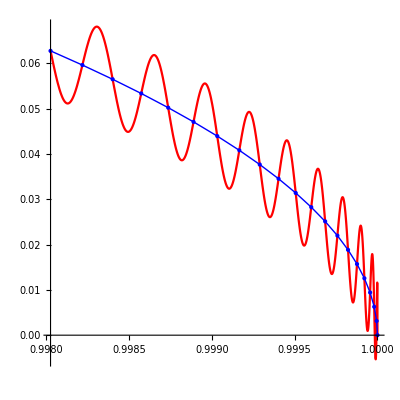

```mathematica
Segments[h[t],{t,0,Pi/50},1000/50,AspectRatio->1]
```

We’re going to proceed with plug-n-chug to find the number of line segments so it is reasonably straight. And we end up with this:

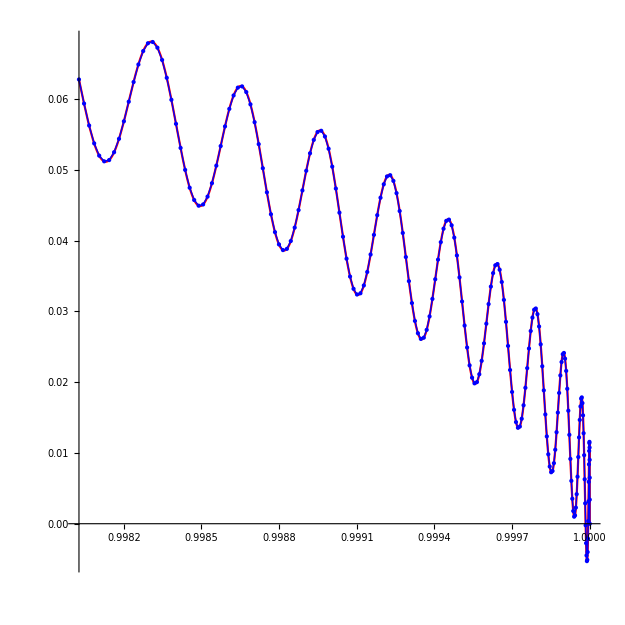

```mathematica
Segments[h[t],{t,0,Pi/50},10000/50,AspectRatio->1]
```

which amounts to 200 segments

And to find the estimation of the total arc length:

```mathematica
Estimate[h[t],{t,0,Pi/50},200]
```

0.400014

#### Exercise 5:

We have the curve of a wire parameterized by f(t)=(t,t^3,t^2), where 0≤t≤1  and we are also given the density of the wire: g(x,y,z)=2x+4y.
Thus, in order to find the mass of this wire, we can use the equation of a path integral:

Mass=∫_C g ds=(∫_0)^1 g(c(t))∥c'(t)∥dt

```mathematica
g[x_, y_, z_] = 2x + 4y;
c[t_] = {t, t^3, t^2};
```

Now to find the derivative of our curve parametrization:

```mathematica
derivative = D[c[t], t]
Norm[%]
```

{1,3 t^2,2 t}

√(1+4 t^2+9 t^4)

Next we plug c(t) into g(x, y, z):

```mathematica
f = Apply[g, c[t]]
```

2 t+4 t^3

And now piece them all together:

```mathematica
Integrate[Apply[g, c[t]]*Norm[D[c[t],t]], {t, 0, 1}]
N[%]
```

1/972 (-132+1338 √14+50 ArcSinh[11/(√5)]-25 Log[5])

5.09149

Thus the mass of our wire is 5.09149  g/cm.